```mathematica
Length[IntegerDigits[%1]]
```

155

```mathematica
code797={797,{2,1},{1,1}};
```

```mathematica
CellularAutomaton[code797,{{{1}},0},1]
```

{{{0,0,0},{0,1,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
ArrayPlot[First[CellularAutomaton[code797, {{{1}}, 0},
                                               {{80}}]]]
```

-Graphics-

```mathematica
Animate[ArrayPlot[First[CellularAutomaton[code797, {{{1}}, 0},{{u}}]]], {u,0,10}]
```

```mathematica
The Game of life
```

```mathematica
Manipulate[
Refresh[
If[oldlen≠len||oldp≠p,
oldlen=len;oldp=p;updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0
];
If[updating||onestep,
t++;
onestep=False;
config = Last[CellularAutomaton[{224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}},If[bg,{config,0},config],{{0,1}}]];
If[config=={},config={{0}}]
];
EventHandler[Dynamic[ArrayPlot[Reverse@config,PlotLabel->Row[{Style["t",Italic]," = "<>ToString[t]}],ImageSize->{400,400},AspectRatio->Automatic]],"MouseClicked":>(If[1<#[[1]]<Length[config]&&1<#[[2]]<Length[First[config]],config[[#[[2]],#[[1]]]]=1-config[[#[[2]],#[[1]]]]]&)[Ceiling@MousePosition["Graphics"]]]

,UpdateInterval->If[updating,0,Infinity]
]
,
{{updating,False,"run simulation"},{True,False}},
Button["update one step",onestep=True,ImageSize->Medium],
Button["reset",updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0,ImageSize->Small],
{{bg,False,"infinite space"},{True,False}},
{{len,50,"edge length"},30,200,10,Appearance->"Labeled",ImageSize->Tiny},
{{oldlen,50},ControlType->None},
{{p,0.1,"initial density"},0,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{oldp,0.1},ControlType->None},
{{t,0},ControlType->None},
{{config,Table[If[RandomReal[]<p,1,0],{50},{50}]},ControlType->None},
{{onestep,False},ControlType->None},
ControlPlacement->Left,
TrackedSymbols:>{updating,onestep,config,len,t,bg,p},AutorunSequencing->{3,5},SynchronousUpdating->True
]
```

```mathematica
Non-totalistic experiments
```

```mathematica
codeGenRule={2974695394759777777777772000000000000000000000034756723452345234598462947,2,{1,1}};
```

```mathematica
Manipulate[
Refresh[
If[oldlen≠len||oldp≠p,
oldlen=len;oldp=p;updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0
];
If[updating||onestep,
t++;
onestep=False;
config = Last[CellularAutomaton[codeGenRule,If[bg,{config,0},config],{{0,1}}]];
If[config=={},config={{0}}]
];
EventHandler[Dynamic[ArrayPlot[Reverse@config,PlotLabel->Row[{Style["t",Italic]," = "<>ToString[t]}],ImageSize->{400,400},AspectRatio->Automatic]],"MouseClicked":>(If[1<#[[1]]<Length[config]&&1<#[[2]]<Length[First[config]],config[[#[[2]],#[[1]]]]=1-config[[#[[2]],#[[1]]]]]&)[Ceiling@MousePosition["Graphics"]]]

,UpdateInterval->If[updating,0,Infinity]
]
,
{{updating,False,"run simulation"},{True,False}},
Button["update one step",onestep=True,ImageSize->Medium],
Button["reset",updating=False;config=Table[If[RandomReal[]<p,1,0],{len},{len}];t=0,ImageSize->Small],
{{bg,False,"infinite space"},{True,False}},
{{len,50,"edge length"},30,200,10,Appearance->"Labeled",ImageSize->Tiny},
{{oldlen,50},ControlType->None},
{{p,0.1,"initial density"},0,1,.01,Appearance->"Labeled",ImageSize->Tiny},
{{oldp,0.1},ControlType->None},
{{t,0},ControlType->None},
{{config,Table[If[RandomReal[]<p,1,0],{50},{50}]},ControlType->None},
{{onestep,False},ControlType->None},
ControlPlacement->Left,
TrackedSymbols:>{updating,onestep,config,len,t,bg,p},AutorunSequencing->{3,5},SynchronousUpdating->True
]
```

```mathematica
combinations = Tuples[{0,1}, 9]
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,1},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1,1},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,1,0,1},{0,0,0,0,0,1,1,1,0},{0,0,0,0,0,1,1,1,1},{0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,1,0},{0,0,0,0,1,0,0,1,1},{0,0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0,1},{0,0,0,0,1,0,1,1,0},{0,0,0,0,1,0,1,1,1},{0,0,0,0,1,1,0,0,0},{0,0,0,0,1,1,0,0,1},{0,0,0,0,1,1,0,1,0},{0,0,0,0,1,1,0,1,1},{0,0,0,0,1,1,1,0,0},{0,0,0,0,1,1,1,0,1},{0,0,0,0,1,1,1,1,0},{0,0,0,0,1,1,1,1,1},{0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,1},{0,0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1,1},{0,0,0,1,0,0,1,0,0},{0,0,0,1,0,0,1,0,1},{0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,1,1,1},{0,0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0,1},{0,0,0,1,0,1,0,1,0},{0,0,0,1,0,1,0,1,1},{0,0,0,1,0,1,1,0,0},{0,0,0,1,0,1,1,0,1},{0,0,0,1,0,1,1,1,0},{0,0,0,1,0,1,1,1,1},{0,0,0,1,1,0,0,0,0},{0,0,0,1,1,0,0,0,1},{0,0,0,1,1,0,0,1,0},{0,0,0,1,1,0,0,1,1},{0,0,0,1,1,0,1,0,0},{0,0,0,1,1,0,1,0,1},{0,0,0,1,1,0,1,1,0},{0,0,0,1,1,0,1,1,1},{0,0,0,1,1,1,0,0,0},{0,0,0,1,1,1,0,0,1},{0,0,0,1,1,1,0,1,0},{0,0,0,1,1,1,0,1,1},{0,0,0,1,1,1,1,0,0},{0,0,0,1,1,1,1,0,1},{0,0,0,1,1,1,1,1,0},{0,0,0,1,1,1,1,1,1},{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1},{0,0,1,0,0,0,0,1,0},{0,0,1,0,0,0,0,1,1},{0,0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0,1},{0,0,1,0,0,0,1,1,0},{0,0,1,0,0,0,1,1,1},{0,0,1,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,1},{0,0,1,0,0,1,0,1,0},{0,0,1,0,0,1,0,1,1},{0,0,1,0,0,1,1,0,0},{0,0,1,0,0,1,1,0,1},{0,0,1,0,0,1,1,1,0},{0,0,1,0,0,1,1,1,1},{0,0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0,1},{0,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,0,1,1},{0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,1,0,1},{0,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,1,1},{0,0,1,0,1,1,0,0,0},{0,0,1,0,1,1,0,0,1},{0,0,1,0,1,1,0,1,0},{0,0,1,0,1,1,0,1,1},{0,0,1,0,1,1,1,0,0},{0,0,1,0,1,1,1,0,1},{0,0,1,0,1,1,1,1,0},{0,0,1,0,1,1,1,1,1},{0,0,1,1,0,0,0,0,0},{0,0,1,1,0,0,0,0,1},{0,0,1,1,0,0,0,1,0},{0,0,1,1,0,0,0,1,1},{0,0,1,1,0,0,1,0,0},{0,0,1,1,0,0,1,0,1},{0,0,1,1,0,0,1,1,0},{0,0,1,1,0,0,1,1,1},{0,0,1,1,0,1,0,0,0},{0,0,1,1,0,1,0,0,1},{0,0,1,1,0,1,0,1,0},{0,0,1,1,0,1,0,1,1},{0,0,1,1,0,1,1,0,0},{0,0,1,1,0,1,1,0,1},{0,0,1,1,0,1,1,1,0},{0,0,1,1,0,1,1,1,1},{0,0,1,1,1,0,0,0,0},{0,0,1,1,1,0,0,0,1},{0,0,1,1,1,0,0,1,0},{0,0,1,1,1,0,0,1,1},{0,0,1,1,1,0,1,0,0},{0,0,1,1,1,0,1,0,1},{0,0,1,1,1,0,1,1,0},{0,0,1,1,1,0,1,1,1},{0,0,1,1,1,1,0,0,0},{0,0,1,1,1,1,0,0,1},{0,0,1,1,1,1,0,1,0},{0,0,1,1,1,1,0,1,1},{0,0,1,1,1,1,1,0,0},{0,0,1,1,1,1,1,0,1},{0,0,1,1,1,1,1,1,0},{0,0,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,1,1},{0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,1,0,1},{0,1,0,0,0,0,1,1,0},{0,1,0,0,0,0,1,1,1},{0,1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0,1},{0,1,0,0,0,1,0,1,0},{0,1,0,0,0,1,0,1,1},{0,1,0,0,0,1,1,0,0},{0,1,0,0,0,1,1,0,1},{0,1,0,0,0,1,1,1,0},{0,1,0,0,0,1,1,1,1},{0,1,0,0,1,0,0,0,0},{0,1,0,0,1,0,0,0,1},{0,1,0,0,1,0,0,1,0},{0,1,0,0,1,0,0,1,1},{0,1,0,0,1,0,1,0,0},{0,1,0,0,1,0,1,0,1},{0,1,0,0,1,0,1,1,0},{0,1,0,0,1,0,1,1,1},{0,1,0,0,1,1,0,0,0},{0,1,0,0,1,1,0,0,1},{0,1,0,0,1,1,0,1,0},{0,1,0,0,1,1,0,1,1},{0,1,0,0,1,1,1,0,0},{0,1,0,0,1,1,1,0,1},{0,1,0,0,1,1,1,1,0},{0,1,0,0,1,1,1,1,1},{0,1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,1},{0,1,0,1,0,0,0,1,0},{0,1,0,1,0,0,0,1,1},{0,1,0,1,0,0,1,0,0},{0,1,0,1,0,0,1,0,1},{0,1,0,1,0,0,1,1,0},{0,1,0,1,0,0,1,1,1},{0,1,0,1,0,1,0,0,0},{0,1,0,1,0,1,0,0,1},{0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,1,1},{0,1,0,1,0,1,1,0,0},{0,1,0,1,0,1,1,0,1},{0,1,0,1,0,1,1,1,0},{0,1,0,1,0,1,1,1,1},{0,1,0,1,1,0,0,0,0},{0,1,0,1,1,0,0,0,1},{0,1,0,1,1,0,0,1,0},{0,1,0,1,1,0,0,1,1},{0,1,0,1,1,0,1,0,0},{0,1,0,1,1,0,1,0,1},{0,1,0,1,1,0,1,1,0},{0,1,0,1,1,0,1,1,1},{0,1,0,1,1,1,0,0,0},{0,1,0,1,1,1,0,0,1},{0,1,0,1,1,1,0,1,0},{0,1,0,1,1,1,0,1,1},{0,1,0,1,1,1,1,0,0},{0,1,0,1,1,1,1,0,1},{0,1,0,1,1,1,1,1,0},{0,1,0,1,1,1,1,1,1},{0,1,1,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,1},{0,1,1,0,0,0,0,1,0},{0,1,1,0,0,0,0,1,1},{0,1,1,0,0,0,1,0,0},{0,1,1,0,0,0,1,0,1},{0,1,1,0,0,0,1,1,0},{0,1,1,0,0,0,1,1,1},{0,1,1,0,0,1,0,0,0},{0,1,1,0,0,1,0,0,1},{0,1,1,0,0,1,0,1,0},{0,1,1,0,0,1,0,1,1},{0,1,1,0,0,1,1,0,0},{0,1,1,0,0,1,1,0,1},{0,1,1,0,0,1,1,1,0},{0,1,1,0,0,1,1,1,1},{0,1,1,0,1,0,0,0,0},{0,1,1,0,1,0,0,0,1},{0,1,1,0,1,0,0,1,0},{0,1,1,0,1,0,0,1,1},{0,1,1,0,1,0,1,0,0},{0,1,1,0,1,0,1,0,1},{0,1,1,0,1,0,1,1,0},{0,1,1,0,1,0,1,1,1},{0,1,1,0,1,1,0,0,0},{0,1,1,0,1,1,0,0,1},{0,1,1,0,1,1,0,1,0},{0,1,1,0,1,1,0,1,1},{0,1,1,0,1,1,1,0,0},{0,1,1,0,1,1,1,0,1},{0,1,1,0,1,1,1,1,0},{0,1,1,0,1,1,1,1,1},{0,1,1,1,0,0,0,0,0},{0,1,1,1,0,0,0,0,1},{0,1,1,1,0,0,0,1,0},{0,1,1,1,0,0,0,1,1},{0,1,1,1,0,0,1,0,0},{0,1,1,1,0,0,1,0,1},{0,1,1,1,0,0,1,1,0},{0,1,1,1,0,0,1,1,1},{0,1,1,1,0,1,0,0,0},{0,1,1,1,0,1,0,0,1},{0,1,1,1,0,1,0,1,0},{0,1,1,1,0,1,0,1,1},{0,1,1,1,0,1,1,0,0},{0,1,1,1,0,1,1,0,1},{0,1,1,1,0,1,1,1,0},{0,1,1,1,0,1,1,1,1},{0,1,1,1,1,0,0,0,0},{0,1,1,1,1,0,0,0,1},{0,1,1,1,1,0,0,1,0},{0,1,1,1,1,0,0,1,1},{0,1,1,1,1,0,1,0,0},{0,1,1,1,1,0,1,0,1},{0,1,1,1,1,0,1,1,0},{0,1,1,1,1,0,1,1,1},{0,1,1,1,1,1,0,0,0},{0,1,1,1,1,1,0,0,1},{0,1,1,1,1,1,0,1,0},{0,1,1,1,1,1,0,1,1},{0,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,1,0,1},{0,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,1,1},{1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,1,1,0},{1,0,0,0,0,0,1,1,1},{1,0,0,0,0,1,0,0,0},{1,0,0,0,0,1,0,0,1},{1,0,0,0,0,1,0,1,0},{1,0,0,0,0,1,0,1,1},{1,0,0,0,0,1,1,0,0},{1,0,0,0,0,1,1,0,1},{1,0,0,0,0,1,1,1,0},{1,0,0,0,0,1,1,1,1},{1,0,0,0,1,0,0,0,0},{1,0,0,0,1,0,0,0,1},{1,0,0,0,1,0,0,1,0},{1,0,0,0,1,0,0,1,1},{1,0,0,0,1,0,1,0,0},{1,0,0,0,1,0,1,0,1},{1,0,0,0,1,0,1,1,0},{1,0,0,0,1,0,1,1,1},{1,0,0,0,1,1,0,0,0},{1,0,0,0,1,1,0,0,1},{1,0,0,0,1,1,0,1,0},{1,0,0,0,1,1,0,1,1},{1,0,0,0,1,1,1,0,0},{1,0,0,0,1,1,1,0,1},{1,0,0,0,1,1,1,1,0},{1,0,0,0,1,1,1,1,1},{1,0,0,1,0,0,0,0,0},{1,0,0,1,0,0,0,0,1},{1,0,0,1,0,0,0,1,0},{1,0,0,1,0,0,0,1,1},{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,1},{1,0,0,1,0,0,1,1,0},{1,0,0,1,0,0,1,1,1},{1,0,0,1,0,1,0,0,0},{1,0,0,1,0,1,0,0,1},{1,0,0,1,0,1,0,1,0},{1,0,0,1,0,1,0,1,1},{1,0,0,1,0,1,1,0,0},{1,0,0,1,0,1,1,0,1},{1,0,0,1,0,1,1,1,0},{1,0,0,1,0,1,1,1,1},{1,0,0,1,1,0,0,0,0},{1,0,0,1,1,0,0,0,1},{1,0,0,1,1,0,0,1,0},{1,0,0,1,1,0,0,1,1},{1,0,0,1,1,0,1,0,0},{1,0,0,1,1,0,1,0,1},{1,0,0,1,1,0,1,1,0},{1,0,0,1,1,0,1,1,1},{1,0,0,1,1,1,0,0,0},{1,0,0,1,1,1,0,0,1},{1,0,0,1,1,1,0,1,0},{1,0,0,1,1,1,0,1,1},{1,0,0,1,1,1,1,0,0},{1,0,0,1,1,1,1,0,1},{1,0,0,1,1,1,1,1,0},{1,0,0,1,1,1,1,1,1},{1,0,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,1},{1,0,1,0,0,0,0,1,0},{1,0,1,0,0,0,0,1,1},{1,0,1,0,0,0,1,0,0},{1,0,1,0,0,0,1,0,1},{1,0,1,0,0,0,1,1,0},{1,0,1,0,0,0,1,1,1},{1,0,1,0,0,1,0,0,0},{1,0,1,0,0,1,0,0,1},{1,0,1,0,0,1,0,1,0},{1,0,1,0,0,1,0,1,1},{1,0,1,0,0,1,1,0,0},{1,0,1,0,0,1,1,0,1},{1,0,1,0,0,1,1,1,0},{1,0,1,0,0,1,1,1,1},{1,0,1,0,1,0,0,0,0},{1,0,1,0,1,0,0,0,1},{1,0,1,0,1,0,0,1,0},{1,0,1,0,1,0,0,1,1},{1,0,1,0,1,0,1,0,0},{1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,1,1,0},{1,0,1,0,1,0,1,1,1},{1,0,1,0,1,1,0,0,0},{1,0,1,0,1,1,0,0,1},{1,0,1,0,1,1,0,1,0},{1,0,1,0,1,1,0,1,1},{1,0,1,0,1,1,1,0,0},{1,0,1,0,1,1,1,0,1},{1,0,1,0,1,1,1,1,0},{1,0,1,0,1,1,1,1,1},{1,0,1,1,0,0,0,0,0},{1,0,1,1,0,0,0,0,1},{1,0,1,1,0,0,0,1,0},{1,0,1,1,0,0,0,1,1},{1,0,1,1,0,0,1,0,0},{1,0,1,1,0,0,1,0,1},{1,0,1,1,0,0,1,1,0},{1,0,1,1,0,0,1,1,1},{1,0,1,1,0,1,0,0,0},{1,0,1,1,0,1,0,0,1},{1,0,1,1,0,1,0,1,0},{1,0,1,1,0,1,0,1,1},{1,0,1,1,0,1,1,0,0},{1,0,1,1,0,1,1,0,1},{1,0,1,1,0,1,1,1,0},{1,0,1,1,0,1,1,1,1},{1,0,1,1,1,0,0,0,0},{1,0,1,1,1,0,0,0,1},{1,0,1,1,1,0,0,1,0},{1,0,1,1,1,0,0,1,1},{1,0,1,1,1,0,1,0,0},{1,0,1,1,1,0,1,0,1},{1,0,1,1,1,0,1,1,0},{1,0,1,1,1,0,1,1,1},{1,0,1,1,1,1,0,0,0},{1,0,1,1,1,1,0,0,1},{1,0,1,1,1,1,0,1,0},{1,0,1,1,1,1,0,1,1},{1,0,1,1,1,1,1,0,0},{1,0,1,1,1,1,1,0,1},{1,0,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,1,0,0},{1,1,0,0,0,0,1,0,1},{1,1,0,0,0,0,1,1,0},{1,1,0,0,0,0,1,1,1},{1,1,0,0,0,1,0,0,0},{1,1,0,0,0,1,0,0,1},{1,1,0,0,0,1,0,1,0},{1,1,0,0,0,1,0,1,1},{1,1,0,0,0,1,1,0,0},{1,1,0,0,0,1,1,0,1},{1,1,0,0,0,1,1,1,0},{1,1,0,0,0,1,1,1,1},{1,1,0,0,1,0,0,0,0},{1,1,0,0,1,0,0,0,1},{1,1,0,0,1,0,0,1,0},{1,1,0,0,1,0,0,1,1},{1,1,0,0,1,0,1,0,0},{1,1,0,0,1,0,1,0,1},{1,1,0,0,1,0,1,1,0},{1,1,0,0,1,0,1,1,1},{1,1,0,0,1,1,0,0,0},{1,1,0,0,1,1,0,0,1},{1,1,0,0,1,1,0,1,0},{1,1,0,0,1,1,0,1,1},{1,1,0,0,1,1,1,0,0},{1,1,0,0,1,1,1,0,1},{1,1,0,0,1,1,1,1,0},{1,1,0,0,1,1,1,1,1},{1,1,0,1,0,0,0,0,0},{1,1,0,1,0,0,0,0,1},{1,1,0,1,0,0,0,1,0},{1,1,0,1,0,0,0,1,1},{1,1,0,1,0,0,1,0,0},{1,1,0,1,0,0,1,0,1},{1,1,0,1,0,0,1,1,0},{1,1,0,1,0,0,1,1,1},{1,1,0,1,0,1,0,0,0},{1,1,0,1,0,1,0,0,1},{1,1,0,1,0,1,0,1,0},{1,1,0,1,0,1,0,1,1},{1,1,0,1,0,1,1,0,0},{1,1,0,1,0,1,1,0,1},{1,1,0,1,0,1,1,1,0},{1,1,0,1,0,1,1,1,1},{1,1,0,1,1,0,0,0,0},{1,1,0,1,1,0,0,0,1},{1,1,0,1,1,0,0,1,0},{1,1,0,1,1,0,0,1,1},{1,1,0,1,1,0,1,0,0},{1,1,0,1,1,0,1,0,1},{1,1,0,1,1,0,1,1,0},{1,1,0,1,1,0,1,1,1},{1,1,0,1,1,1,0,0,0},{1,1,0,1,1,1,0,0,1},{1,1,0,1,1,1,0,1,0},{1,1,0,1,1,1,0,1,1},{1,1,0,1,1,1,1,0,0},{1,1,0,1,1,1,1,0,1},{1,1,0,1,1,1,1,1,0},{1,1,0,1,1,1,1,1,1},{1,1,1,0,0,0,0,0,0},{1,1,1,0,0,0,0,0,1},{1,1,1,0,0,0,0,1,0},{1,1,1,0,0,0,0,1,1},{1,1,1,0,0,0,1,0,0},{1,1,1,0,0,0,1,0,1},{1,1,1,0,0,0,1,1,0},{1,1,1,0,0,0,1,1,1},{1,1,1,0,0,1,0,0,0},{1,1,1,0,0,1,0,0,1},{1,1,1,0,0,1,0,1,0},{1,1,1,0,0,1,0,1,1},{1,1,1,0,0,1,1,0,0},{1,1,1,0,0,1,1,0,1},{1,1,1,0,0,1,1,1,0},{1,1,1,0,0,1,1,1,1},{1,1,1,0,1,0,0,0,0},{1,1,1,0,1,0,0,0,1},{1,1,1,0,1,0,0,1,0},{1,1,1,0,1,0,0,1,1},{1,1,1,0,1,0,1,0,0},{1,1,1,0,1,0,1,0,1},{1,1,1,0,1,0,1,1,0},{1,1,1,0,1,0,1,1,1},{1,1,1,0,1,1,0,0,0},{1,1,1,0,1,1,0,0,1},{1,1,1,0,1,1,0,1,0},{1,1,1,0,1,1,0,1,1},{1,1,1,0,1,1,1,0,0},{1,1,1,0,1,1,1,0,1},{1,1,1,0,1,1,1,1,0},{1,1,1,0,1,1,1,1,1},{1,1,1,1,0,0,0,0,0},{1,1,1,1,0,0,0,0,1},{1,1,1,1,0,0,0,1,0},{1,1,1,1,0,0,0,1,1},{1,1,1,1,0,0,1,0,0},{1,1,1,1,0,0,1,0,1},{1,1,1,1,0,0,1,1,0},{1,1,1,1,0,0,1,1,1},{1,1,1,1,0,1,0,0,0},{1,1,1,1,0,1,0,0,1},{1,1,1,1,0,1,0,1,0},{1,1,1,1,0,1,0,1,1},{1,1,1,1,0,1,1,0,0},{1,1,1,1,0,1,1,0,1},{1,1,1,1,0,1,1,1,0},{1,1,1,1,0,1,1,1,1},{1,1,1,1,1,0,0,0,0},{1,1,1,1,1,0,0,0,1},{1,1,1,1,1,0,0,1,0},{1,1,1,1,1,0,0,1,1},{1,1,1,1,1,0,1,0,0},{1,1,1,1,1,0,1,0,1},{1,1,1,1,1,0,1,1,0},{1,1,1,1,1,0,1,1,1},{1,1,1,1,1,1,0,0,0},{1,1,1,1,1,1,0,0,1},{1,1,1,1,1,1,0,1,0},{1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,1,1}}

```mathematica
Length[combinations]
```

512

```mathematica
2^Length[combinations]
```

13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084096

```mathematica
binMax = IntegerDigits[2^Length[combinations],2]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[IntegerDigits[2^Length[combinations],2]]
```

513

```mathematica
s = {{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,0}}
```

{{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,0}}

```mathematica
Partition[#, 3]& /@ s
```

{{{1,0,0},{1,0,0},{1,0,0}},{{1,0,0},{1,0,0},{1,0,1}}}

```mathematica
s = {{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,1}}
```

{{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,1,0,1}}

```mathematica
indexes = Partition[#, 3]& /@ combinations
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,1,0}},{{0,0,0},{0,0,0},{0,1,1}},{{0,0,0},{0,0,0},{1,0,0}},502,{{1,1,1},{1,1,1},{0,1,1}},{{1,1,1},{1,1,1},{1,0,0}},{{1,1,1},{1,1,1},{1,0,1}},{{1,1,1},{1,1,1},{1,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}
 |  |  |  |

```mathematica
ruleNumberDigits = Array[0&,512]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ruleNumberDigitsDynamic = Dynamic[rn]
```

```mathematica
{False,True}[[
ruleNumberDigits[[0]]+1]]
```

Part::pkspec1: The expression 1 + List cannot be used as a part specification.

{False,True}⟦1+List⟧

```mathematica
ruleNumberDigits[[0]]
```

List

```mathematica
{False,True}[[1]]
```

False

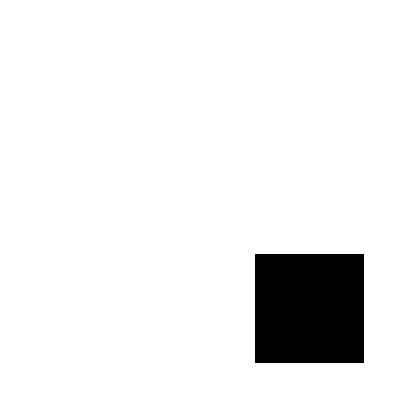
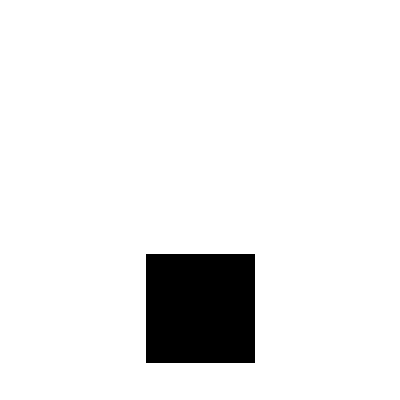
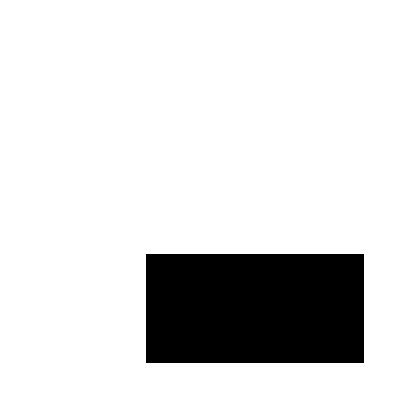
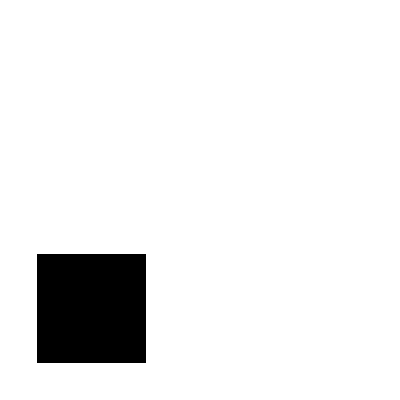
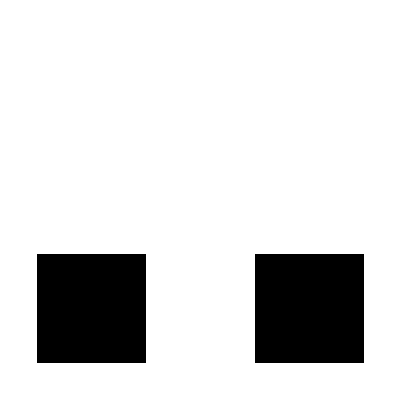
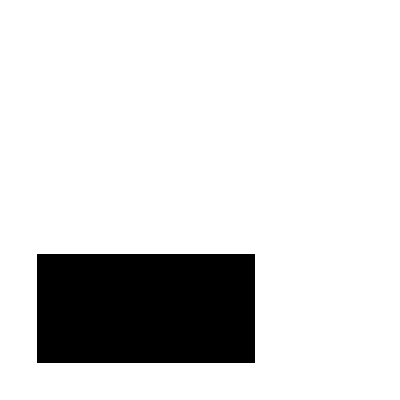
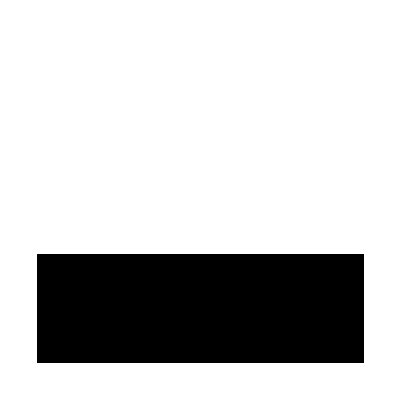
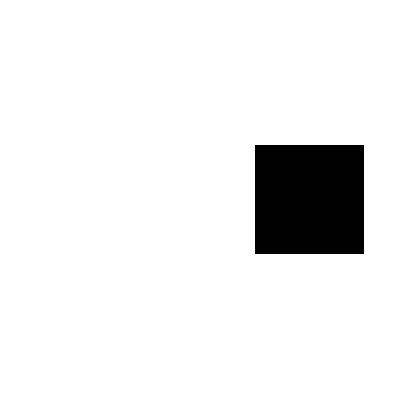
{{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False},{-Graphics-,,False}}

```mathematica
MapIndexed[
Join[
{ArrayPlot[#1, ImageSize->Tiny]},
{Checkbox[Dynamic[
{False,True}[[
ruleNumberDigits[[#2[[1]]]]+1]] 

]]},
{
{False,True}[[
ruleNumberDigits[[#2[[1]]]]+1]]
}
]& , 
indexes]
```

```mathematica
Manipulator[]
```

```mathematica
Find a rule number in the above space and generate the manipulate for it
```